```mathematica
sqrLen[v_]:=v.v
```

```mathematica
ray[s_,d_,t_]:=s+d*t
```

```mathematica
Simplify[Solve[sqrLen[{px,py,pz}-ray[{sx,sy,sz},{dx,dy,dz},t]]-r*r==0,t]]
```

{{t→1/(dx^2+dy^2+dz^2)(dx px+dy py+dz pz-dx sx-dy sy-dz sz-1/2 √(4 (dx (px-sx)+dy (py-sy)+dz (pz-sz))^2-4 (dx^2+dy^2+dz^2) (px^2+py^2+pz^2-r^2-2 px sx+sx^2-2 py sy+sy^2-2 pz sz+sz^2)))},{t→1/(dx^2+dy^2+dz^2)(dx px+dy py+dz pz-dx sx-dy sy-dz sz+1/2 √(4 (dx (px-sx)+dy (py-sy)+dz (pz-sz))^2-4 (dx^2+dy^2+dz^2) (px^2+py^2+pz^2-r^2-2 px sx+sx^2-2 py sy+sy^2-2 pz sz+sz^2)))}}

```mathematica
Simplify[Solve[sqrLen[{px,py,pz}-ray[{0,0,0},{1,0,0},t]]-r*r==0,t]]
```

{{t→px-√(-py^2-pz^2+r^2)},{t→px+√(-py^2-pz^2+r^2)}}

```mathematica
tForDtoP[p_,r_,sol_]:=p[[1]]+sol*√(-p[[2]]^2-p[[3]]^2+r^2)
```

```mathematica
tForDtoP2[p_,r_]:={tForDtoP[p,r,-1],tForDtoP[p,r,1]}
```

```mathematica
tForDtoP[ray[{sx,sy,sz},{dx,dy,dz},l],r,sol]
```

dx l+sx+sol √(r^2-(dy l+sy)^2-(dz l+sz)^2)

```mathematica
D[tForDtoP[ray[{sx,sy,sz},{dx,dy,dz},l],r,sol],l]
```

dx+(sol (-2 dy (dy l+sy)-2 dz (dz l+sz)))/(2 √(r^2-(dy l+sy)^2-(dz l+sz)^2))

```mathematica
cylD[sx_,sy_,sz_,dx_,dy_,dz_,r_,l_,sol_]:=dx+(sol (-2 dy (dy l+sy)-2 dz (dz l+sz)))/(2 √(r^2-(dy l+sy)^2-(dz l+sz)^2))
```

```mathematica
Simplify[Solve[dx-(-2 dy (dy l+sy)-2 dz (dz l+sz))/(2 √(r^2-(dy l+sy)^2-(dz l+sz)^2))==0,l]]
```

{{l→-1/((dy^2+dz^2) (dx^2+dy^2+dz^2))(dy^3 sy+dy dz^2 sy+dy^2 dz sz+dz^3 sz+dx^2 (dy sy+dz sz)+√(dx^2 (dx^2+dy^2+dz^2) (dz^2 (r^2-sy^2)+2 dy dz sy sz+dy^2 (r^2-sz^2))))},{l→-1/((dy^2+dz^2) (dx^2+dy^2+dz^2))(dy^3 sy+dy dz^2 sy+dy^2 dz sz+dz^3 sz+dx^2 (dy sy+dz sz)-√(dx^2 (dx^2+dy^2+dz^2) (dz^2 (r^2-sy^2)+2 dy dz sy sz+dy^2 (r^2-sz^2))))}}

```mathematica
Solve[r^2-(-dy l+sy)^2-(-dz l+sz)^2==0,l]
```

{{l→(dy sy+dz sz-√(dy^2 r^2+dz^2 r^2-dz^2 sy^2+2 dy dz sy sz-dy^2 sz^2))/(dy^2+dz^2)},{l→(dy sy+dz sz+√(dy^2 r^2+dz^2 r^2-dz^2 sy^2+2 dy dz sy sz-dy^2 sz^2))/(dy^2+dz^2)}}

```mathematica
cylPoly[sx_,sy_,sz_,dx_,dy_,dz_,r_,l_]:=r^2-(dy l+sy)^2-(dz l+sz)^2
```

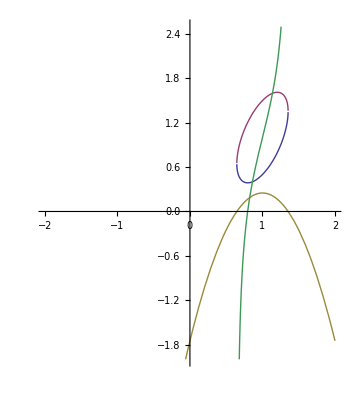

```mathematica
Plot[{tForDtoP[ray[{0,1,1},{1,-1,-1},l],0.5,-1],tForDtoP[ray[{0,1,1},{1,-1,-1},l],0.5,1],cylPoly[0,1,1,1,-1,-1,0.5,l],cylD[0,1,1,1,-1,-1,0.5,l,-1]},{l,-2,2},PlotRange->{-2,2.5},AspectRatio->Automatic]
```

```mathematica
Solve[tForDtoP[ray[{sx,sy,sz},{dx,dy,dz},t],r,1]==l,t]
```

{{t→1/(2 (dx^2+dy^2+dz^2))(2 dx l-2 dx sx-2 dy sy-2 dz sz-√((-2 dx l+2 dx sx+2 dy sy+2 dz sz)^2-4 (dx^2+dy^2+dz^2) (l^2-r^2-2 l sx+sx^2+sy^2+sz^2)))},{t→1/(2 (dx^2+dy^2+dz^2))(2 dx l-2 dx sx-2 dy sy-2 dz sz+√((-2 dx l+2 dx sx+2 dy sy+2 dz sz)^2-4 (dx^2+dy^2+dz^2) (l^2-r^2-2 l sx+sx^2+sy^2+sz^2)))}}

```mathematica
Solve[(-2 dx l+2 dx sx+2 dy sy+2 dz sz)^2-4 (dx^2+dy^2+dz^2) (l^2-r^2-2 l sx+sx^2+sy^2+sz^2)==0,l]
```

{{l→1/(2 (-dy^2-dz^2))(-2 dy^2 sx-2 dz^2 sx+2 dx dy sy+2 dx dz sz-√((2 dy^2 sx+2 dz^2 sx-2 dx dy sy-2 dx dz sz)^2-4 (-dy^2-dz^2) (dx^2 r^2+dy^2 r^2+dz^2 r^2-dy^2 sx^2-dz^2 sx^2+2 dx dy sx sy-dx^2 sy^2-dz^2 sy^2+2 dx dz sx sz+2 dy dz sy sz-dx^2 sz^2-dy^2 sz^2)))},{l→1/(2 (-dy^2-dz^2))(-2 dy^2 sx-2 dz^2 sx+2 dx dy sy+2 dx dz sz+√((2 dy^2 sx+2 dz^2 sx-2 dx dy sy-2 dx dz sz)^2-4 (-dy^2-dz^2) (dx^2 r^2+dy^2 r^2+dz^2 r^2-dy^2 sx^2-dz^2 sx^2+2 dx dy sx sy-dx^2 sy^2-dz^2 sy^2+2 dx dz sx sz+2 dy dz sy sz-dx^2 sz^2-dy^2 sz^2)))}}

```mathematica
lerp[a_,b_,t_]:=a+(b-a)*t
```

```mathematica
bq[c1_,c2_,h_,t_]:=lerp[lerp[c1,h,t],lerp[h,c2,t],t]
```

```mathematica
bc[c1_,c2_,h1_,h2_,t_]:=lerp[lerp[lerp[c1,h1,t],lerp[h1,h2,t],t],lerp[lerp[h1,h2,t],lerp[h2,c2,t],t],t]
```

```mathematica
Simplify[D[sqrLen[{px,py,pz}-bq[{c1x,c1y,c1z},{c2x,c2y,c2z},{hx,hy,hz},t]]-r*r,t]]
```

4 ((hx+c1x (-1+t)+c2x t-2 hx t) (-px+c1x (-1+t)^2+t (2 hx+c2x t-2 hx t))+(hy+c1y (-1+t)+c2y t-2 hy t) (-py+c1y (-1+t)^2+t (2 hy+c2y t-2 hy t))+(hz+c1z (-1+t)+c2z t-2 hz t) (-pz+c1z (-1+t)^2+t (2 hz+c2z t-2 hz t)))

```mathematica
tForDtoBC[c1_,c2_,h_,r_,t_,sol_]=Simplify[tForDtoP[bq[{c1[[1]],c1[[2]],c1[[3]]},{c2[[1]],c2[[2]],c2[[3]]},{h[[1]],h[[2]],h[[3]]},t],r,sol]]
```

Part::partd: Part specification c1 ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification c1 ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification c1 ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

c1⟦1⟧-2 t c1⟦1⟧+t^2 c1⟦1⟧+t^2 c2⟦1⟧+2 t h⟦1⟧-2 t^2 h⟦1⟧+sol √(r^2-((-1+t)^2 c1⟦2⟧+t (t c2⟦2⟧-2 (-1+t) h⟦2⟧))^2-((-1+t)^2 c1⟦3⟧+t (t c2⟦3⟧-2 (-1+t) h⟦3⟧))^2)

```mathematica
Collect[c1⟦1⟧-2 t c1⟦1⟧+t^2 c1⟦1⟧+t^2 c2⟦1⟧+2 t h⟦1⟧-2 t^2 h⟦1⟧,t]
```

Part::partd: Part specification c1 ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

c1⟦1⟧+t^2 (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧)+t (-2 c1⟦1⟧+2 h⟦1⟧)

```mathematica
tForDtoBCD1[c1_,c2_,h_,r_,t_,sol_]=Id[Simplify[D[c1⟦1⟧-2 t c1⟦1⟧+t^2 c1⟦1⟧+t^2 c2⟦1⟧+2 t h⟦1⟧-2 t^2 h⟦1⟧+sol √(r^2-((-1+t)^2 c1⟦2⟧+t (t c2⟦2⟧-2 (-1+t) h⟦2⟧))^2-((-1+t)^2 c1⟦3⟧+t (t c2⟦3⟧-2 (-1+t) h⟦3⟧))^2),t]]]
```

Part::partd: Part specification c1 ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

-2 c1⟦1⟧+2 t c1⟦1⟧+2 t c2⟦1⟧+2 h⟦1⟧-4 t h⟦1⟧+(sol (-4 ((-1+t) c1⟦2⟧+t c2⟦2⟧+(1-2 t) h⟦2⟧) ((-1+t)^2 c1⟦2⟧+t (t c2⟦2⟧-2 (-1+t) h⟦2⟧))-4 ((-1+t) c1⟦3⟧+t c2⟦3⟧+(1-2 t) h⟦3⟧) ((-1+t)^2 c1⟦3⟧+t (t c2⟦3⟧-2 (-1+t) h⟦3⟧))))/(2 √(r^2-((-1+t)^2 c1⟦2⟧+t (t c2⟦2⟧-2 (-1+t) h⟦2⟧))^2-((-1+t)^2 c1⟦3⟧+t (t c2⟦3⟧-2 (-1+t) h⟦3⟧))^2))

```mathematica
tForDtoBCD1Alt[c1_,c2_,h_,r_,t_,sol_]:=(-2 c1⟦1⟧+2 t c1⟦1⟧+2 t c2⟦1⟧+2 h⟦1⟧-4 t h⟦1⟧)*(2 √(r^2-((-1+t)^2 c1⟦2⟧+t (t c2⟦2⟧-2 (-1+t) h⟦2⟧))^2-((-1+t)^2 c1⟦3⟧+t (t c2⟦3⟧-2 (-1+t) h⟦3⟧))^2))+(sol (-4 ((-1+t) c1⟦2⟧+t c2⟦2⟧+(1-2 t) h⟦2⟧) ((-1+t)^2 c1⟦2⟧+t (t c2⟦2⟧-2 (-1+t) h⟦2⟧))-4 ((-1+t) c1⟦3⟧+t c2⟦3⟧+(1-2 t) h⟦3⟧) ((-1+t)^2 c1⟦3⟧+t (t c2⟦3⟧-2 (-1+t) h⟦3⟧))))
```

```mathematica
Collect[(-2 c1⟦1⟧+2 t c1⟦1⟧+2 t c2⟦1⟧+2 h⟦1⟧-4 t h⟦1⟧)*(2 √(r^2-((-1+t)^2 c1⟦2⟧+t (t c2⟦2⟧-2 (-1+t) h⟦2⟧))^2-((-1+t)^2 c1⟦3⟧+t (t c2⟦3⟧-2 (-1+t) h⟦3⟧))^2))+(sol (-4 ((-1+t) c1⟦2⟧+t c2⟦2⟧+(1-2 t) h⟦2⟧) ((-1+t)^2 c1⟦2⟧+t (t c2⟦2⟧-2 (-1+t) h⟦2⟧))-4 ((-1+t) c1⟦3⟧+t c2⟦3⟧+(1-2 t) h⟦3⟧) ((-1+t)^2 c1⟦3⟧+t (t c2⟦3⟧-2 (-1+t) h⟦3⟧)))),t]
```

Part::partd: Part specification c1 ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification c2 ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

4 sol c1⟦2⟧^2+4 sol c1⟦3⟧^2-4 sol c1⟦2⟧ h⟦2⟧-4 sol c1⟦3⟧ h⟦3⟧+t^3 (-4 sol c1⟦2⟧^2-4 sol c1⟦3⟧^2-8 sol c1⟦2⟧ c2⟦2⟧-4 sol c2⟦2⟧^2-8 sol c1⟦3⟧ c2⟦3⟧-4 sol c2⟦3⟧^2+16 sol c1⟦2⟧ h⟦2⟧+16 sol c2⟦2⟧ h⟦2⟧-16 sol h⟦2⟧^2+16 sol c1⟦3⟧ h⟦3⟧+16 sol c2⟦3⟧ h⟦3⟧-16 sol h⟦3⟧^2)+t^2 (12 sol c1⟦2⟧^2+12 sol c1⟦3⟧^2+12 sol c1⟦2⟧ c2⟦2⟧+12 sol c1⟦3⟧ c2⟦3⟧-36 sol c1⟦2⟧ h⟦2⟧-12 sol c2⟦2⟧ h⟦2⟧+24 sol h⟦2⟧^2-36 sol c1⟦3⟧ h⟦3⟧-12 sol c2⟦3⟧ h⟦3⟧+24 sol h⟦3⟧^2)-4 c1⟦1⟧ √(r^2-((-1+t)^2 c1⟦2⟧+t (t c2⟦2⟧-2 (-1+t) h⟦2⟧))^2-((-1+t)^2 c1⟦3⟧+t (t c2⟦3⟧-2 (-1+t) h⟦3⟧))^2)+4 h⟦1⟧ √(r^2-((-1+t)^2 c1⟦2⟧+t (t c2⟦2⟧-2 (-1+t) h⟦2⟧))^2-((-1+t)^2 c1⟦3⟧+t (t c2⟦3⟧-2 (-1+t) h⟦3⟧))^2)+t (-12 sol c1⟦2⟧^2-12 sol c1⟦3⟧^2-4 sol c1⟦2⟧ c2⟦2⟧-4 sol c1⟦3⟧ c2⟦3⟧+24 sol c1⟦2⟧ h⟦2⟧-8 sol h⟦2⟧^2+24 sol c1⟦3⟧ h⟦3⟧-8 sol h⟦3⟧^2+4 c1⟦1⟧ √(r^2-((-1+t)^2 c1⟦2⟧+t (t c2⟦2⟧-2 (-1+t) h⟦2⟧))^2-((-1+t)^2 c1⟦3⟧+t (t c2⟦3⟧-2 (-1+t) h⟦3⟧))^2)+4 c2⟦1⟧ √(r^2-((-1+t)^2 c1⟦2⟧+t (t c2⟦2⟧-2 (-1+t) h⟦2⟧))^2-((-1+t)^2 c1⟦3⟧+t (t c2⟦3⟧-2 (-1+t) h⟦3⟧))^2)-8 h⟦1⟧ √(r^2-((-1+t)^2 c1⟦2⟧+t (t c2⟦2⟧-2 (-1+t) h⟦2⟧))^2-((-1+t)^2 c1⟦3⟧+t (t c2⟦3⟧-2 (-1+t) h⟦3⟧))^2))

```mathematica
tForDtoBCD1Alt2[c1_,c2_,h_,r_,t_,sol_]=Collect[Simplify[4 sol c1⟦2⟧^2+4 sol c1⟦3⟧^2-4 sol c1⟦2⟧ h⟦2⟧-4 sol c1⟦3⟧ h⟦3⟧+Integrate[tForDtoBCD2Alt[c1,c2,h,r,t,sol],t]],t]
```

Part::partd: Part specification c1 ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification c1 ⟦ 3 ⟧ is longer than depth of object.

Part::partd: Part specification c1 ⟦ 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

4 sol c1⟦2⟧^2+4 sol c1⟦3⟧^2-4 sol c1⟦2⟧ h⟦2⟧-4 sol c1⟦3⟧ h⟦3⟧-12/5 t^5 (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧) (c1⟦2⟧^2+c1⟦3⟧^2+c2⟦2⟧^2+c2⟦3⟧^2+2 c1⟦2⟧ (c2⟦2⟧-2 h⟦2⟧)-4 c2⟦2⟧ h⟦2⟧+4 h⟦2⟧^2+2 c1⟦3⟧ (c2⟦3⟧-2 h⟦3⟧)-4 c2⟦3⟧ h⟦3⟧+4 h⟦3⟧^2)+t (4 (r^2-c1⟦2⟧^2-c1⟦3⟧^2) (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧)-8 (c1⟦1⟧-h⟦1⟧) (c1⟦2⟧^2-c1⟦2⟧ h⟦2⟧+c1⟦3⟧ (c1⟦3⟧-h⟦3⟧))-4 sol (3 c1⟦2⟧^2+3 c1⟦3⟧^2+c1⟦2⟧ (c2⟦2⟧-6 h⟦2⟧)+c1⟦3⟧ (c2⟦3⟧-6 h⟦3⟧)+2 (h⟦2⟧^2+h⟦3⟧^2)))+t^3 (-4 sol (c1⟦2⟧^2+c1⟦3⟧^2+c2⟦2⟧^2+c2⟦3⟧^2+2 c1⟦2⟧ (c2⟦2⟧-2 h⟦2⟧)-4 c2⟦2⟧ h⟦2⟧+4 h⟦2⟧^2+2 c1⟦3⟧ (c2⟦3⟧-2 h⟦3⟧)-4 c2⟦3⟧ h⟦3⟧+4 h⟦3⟧^2)-8/3 (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧) (3 c1⟦2⟧^2+3 c1⟦3⟧^2+c1⟦2⟧ (c2⟦2⟧-6 h⟦2⟧)+c1⟦3⟧ (c2⟦3⟧-6 h⟦3⟧)+2 (h⟦2⟧^2+h⟦3⟧^2))-8/3 (3 c1⟦3⟧^2 c2⟦1⟧+c1⟦3⟧ c2⟦1⟧ c2⟦3⟧+3 c1⟦2⟧^2 (c2⟦1⟧-3 h⟦1⟧)-9 c1⟦3⟧^2 h⟦1⟧-5 c1⟦3⟧ c2⟦3⟧ h⟦1⟧+3 c2⟦2⟧ h⟦1⟧ h⟦2⟧+2 c2⟦1⟧ h⟦2⟧^2-10 h⟦1⟧ h⟦2⟧^2+c1⟦2⟧ (c2⟦1⟧ (c2⟦2⟧-6 h⟦2⟧)+h⟦1⟧ (-5 c2⟦2⟧+21 h⟦2⟧))-6 c1⟦3⟧ c2⟦1⟧ h⟦3⟧+21 c1⟦3⟧ h⟦1⟧ h⟦3⟧+3 c2⟦3⟧ h⟦1⟧ h⟦3⟧+2 c2⟦1⟧ h⟦3⟧^2-10 h⟦1⟧ h⟦3⟧^2+c1⟦1⟧ (6 c1⟦2⟧^2+6 c1⟦3⟧^2+c1⟦2⟧ (4 c2⟦2⟧-15 h⟦2⟧)-3 c2⟦2⟧ h⟦2⟧+8 h⟦2⟧^2+c1⟦3⟧ (4 c2⟦3⟧-15 h⟦3⟧)-3 c2⟦3⟧ h⟦3⟧+8 h⟦3⟧^2)))+t^4 (4 (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧) (c1⟦2⟧^2+c1⟦3⟧^2+c1⟦2⟧ (c2⟦2⟧-3 h⟦2⟧)-c2⟦2⟧ h⟦2⟧+2 h⟦2⟧^2+c1⟦3⟧ (c2⟦3⟧-3 h⟦3⟧)-c2⟦3⟧ h⟦3⟧+2 h⟦3⟧^2)+2 (3 c1⟦3⟧^2 c2⟦1⟧+3 c1⟦3⟧ c2⟦1⟧ c2⟦3⟧+c1⟦2⟧^2 (3 c2⟦1⟧-7 h⟦1⟧)-7 c1⟦3⟧^2 h⟦1⟧-c2⟦2⟧^2 h⟦1⟧-8 c1⟦3⟧ c2⟦3⟧ h⟦1⟧-c2⟦3⟧^2 h⟦1⟧-3 c2⟦1⟧ c2⟦2⟧ h⟦2⟧+10 c2⟦2⟧ h⟦1⟧ h⟦2⟧+6 c2⟦1⟧ h⟦2⟧^2-16 h⟦1⟧ h⟦2⟧^2+c1⟦2⟧ (3 c2⟦1⟧ (c2⟦2⟧-3 h⟦2⟧)+2 h⟦1⟧ (-4 c2⟦2⟧+11 h⟦2⟧))-9 c1⟦3⟧ c2⟦1⟧ h⟦3⟧-3 c2⟦1⟧ c2⟦3⟧ h⟦3⟧+22 c1⟦3⟧ h⟦1⟧ h⟦3⟧+10 c2⟦3⟧ h⟦1⟧ h⟦3⟧+6 c2⟦1⟧ h⟦3⟧^2-16 h⟦1⟧ h⟦3⟧^2+c1⟦1⟧ (4 c1⟦2⟧^2+4 c1⟦3⟧^2+c2⟦2⟧^2+c2⟦3⟧^2+c1⟦2⟧ (5 c2⟦2⟧-13 h⟦2⟧)-7 c2⟦2⟧ h⟦2⟧+10 h⟦2⟧^2+c1⟦3⟧ (5 c2⟦3⟧-13 h⟦3⟧)-7 c2⟦3⟧ h⟦3⟧+10 h⟦3⟧^2)))+t^2 (8 (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧) (c1⟦2⟧^2-c1⟦2⟧ h⟦2⟧+c1⟦3⟧ (c1⟦3⟧-h⟦3⟧))+12 sol (c1⟦2⟧^2+c1⟦3⟧^2+c1⟦2⟧ (c2⟦2⟧-3 h⟦2⟧)-c2⟦2⟧ h⟦2⟧+2 h⟦2⟧^2+c1⟦3⟧ (c2⟦3⟧-3 h⟦3⟧)-c2⟦3⟧ h⟦3⟧+2 h⟦3⟧^2)+4 (c1⟦3⟧^2 c2⟦1⟧+c1⟦2⟧^2 (c2⟦1⟧-5 h⟦1⟧)-5 c1⟦3⟧^2 h⟦1⟧-c1⟦3⟧ c2⟦3⟧ h⟦1⟧-2 h⟦1⟧ h⟦2⟧^2-c1⟦2⟧ (c2⟦2⟧ h⟦1⟧+(c2⟦1⟧-8 h⟦1⟧) h⟦2⟧)-c1⟦3⟧ c2⟦1⟧ h⟦3⟧+8 c1⟦3⟧ h⟦1⟧ h⟦3⟧-2 h⟦1⟧ h⟦3⟧^2+c1⟦1⟧ (4 c1⟦2⟧^2+4 c1⟦3⟧^2+c1⟦2⟧ (c2⟦2⟧-7 h⟦2⟧)+c1⟦3⟧ (c2⟦3⟧-7 h⟦3⟧)+2 (h⟦2⟧^2+h⟦3⟧^2))))

```mathematica
tForDtoBCD1Alt3[c1_,c2_,h_,r_,t_,sol_]:=4 sol c1⟦2⟧^2+4 sol c1⟦3⟧^2-4 sol c1⟦2⟧ h⟦2⟧-4 sol c1⟦3⟧ h⟦3⟧-12/5 *0*t^5 (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧) (c1⟦2⟧^2+c1⟦3⟧^2+c2⟦2⟧^2+c2⟦3⟧^2+2 c1⟦2⟧ (c2⟦2⟧-2 h⟦2⟧)-4 c2⟦2⟧ h⟦2⟧+4 h⟦2⟧^2+2 c1⟦3⟧ (c2⟦3⟧-2 h⟦3⟧)-4 c2⟦3⟧ h⟦3⟧+4 h⟦3⟧^2)+t (4 (r^2-c1⟦2⟧^2-c1⟦3⟧^2) (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧)-8 (c1⟦1⟧-h⟦1⟧) (c1⟦2⟧^2-c1⟦2⟧ h⟦2⟧+c1⟦3⟧ (c1⟦3⟧-h⟦3⟧))-4 sol (3 c1⟦2⟧^2+3 c1⟦3⟧^2+c1⟦2⟧ (c2⟦2⟧-6 h⟦2⟧)+c1⟦3⟧ (c2⟦3⟧-6 h⟦3⟧)+2 (h⟦2⟧^2+h⟦3⟧^2)))+t^3 (-4 sol (c1⟦2⟧^2+c1⟦3⟧^2+c2⟦2⟧^2+c2⟦3⟧^2+2 c1⟦2⟧ (c2⟦2⟧-2 h⟦2⟧)-4 c2⟦2⟧ h⟦2⟧+4 h⟦2⟧^2+2 c1⟦3⟧ (c2⟦3⟧-2 h⟦3⟧)-4 c2⟦3⟧ h⟦3⟧+4 h⟦3⟧^2)-8/3 (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧) (3 c1⟦2⟧^2+3 c1⟦3⟧^2+c1⟦2⟧ (c2⟦2⟧-6 h⟦2⟧)+c1⟦3⟧ (c2⟦3⟧-6 h⟦3⟧)+2 (h⟦2⟧^2+h⟦3⟧^2))-8/3 (3 c1⟦3⟧^2 c2⟦1⟧+c1⟦3⟧ c2⟦1⟧ c2⟦3⟧+3 c1⟦2⟧^2 (c2⟦1⟧-3 h⟦1⟧)-9 c1⟦3⟧^2 h⟦1⟧-5 c1⟦3⟧ c2⟦3⟧ h⟦1⟧+3 c2⟦2⟧ h⟦1⟧ h⟦2⟧+2 c2⟦1⟧ h⟦2⟧^2-10 h⟦1⟧ h⟦2⟧^2+c1⟦2⟧ (c2⟦1⟧ (c2⟦2⟧-6 h⟦2⟧)+h⟦1⟧ (-5 c2⟦2⟧+21 h⟦2⟧))-6 c1⟦3⟧ c2⟦1⟧ h⟦3⟧+21 c1⟦3⟧ h⟦1⟧ h⟦3⟧+3 c2⟦3⟧ h⟦1⟧ h⟦3⟧+2 c2⟦1⟧ h⟦3⟧^2-10 h⟦1⟧ h⟦3⟧^2+c1⟦1⟧ (6 c1⟦2⟧^2+6 c1⟦3⟧^2+c1⟦2⟧ (4 c2⟦2⟧-15 h⟦2⟧)-3 c2⟦2⟧ h⟦2⟧+8 h⟦2⟧^2+c1⟦3⟧ (4 c2⟦3⟧-15 h⟦3⟧)-3 c2⟦3⟧ h⟦3⟧+8 h⟦3⟧^2)))+t^4 (4 (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧) (c1⟦2⟧^2+c1⟦3⟧^2+c1⟦2⟧ (c2⟦2⟧-3 h⟦2⟧)-c2⟦2⟧ h⟦2⟧+2 h⟦2⟧^2+c1⟦3⟧ (c2⟦3⟧-3 h⟦3⟧)-c2⟦3⟧ h⟦3⟧+2 h⟦3⟧^2)+2 (3 c1⟦3⟧^2 c2⟦1⟧+3 c1⟦3⟧ c2⟦1⟧ c2⟦3⟧+c1⟦2⟧^2 (3 c2⟦1⟧-7 h⟦1⟧)-7 c1⟦3⟧^2 h⟦1⟧-c2⟦2⟧^2 h⟦1⟧-8 c1⟦3⟧ c2⟦3⟧ h⟦1⟧-c2⟦3⟧^2 h⟦1⟧-3 c2⟦1⟧ c2⟦2⟧ h⟦2⟧+10 c2⟦2⟧ h⟦1⟧ h⟦2⟧+6 c2⟦1⟧ h⟦2⟧^2-16 h⟦1⟧ h⟦2⟧^2+c1⟦2⟧ (3 c2⟦1⟧ (c2⟦2⟧-3 h⟦2⟧)+2 h⟦1⟧ (-4 c2⟦2⟧+11 h⟦2⟧))-9 c1⟦3⟧ c2⟦1⟧ h⟦3⟧-3 c2⟦1⟧ c2⟦3⟧ h⟦3⟧+22 c1⟦3⟧ h⟦1⟧ h⟦3⟧+10 c2⟦3⟧ h⟦1⟧ h⟦3⟧+6 c2⟦1⟧ h⟦3⟧^2-16 h⟦1⟧ h⟦3⟧^2+c1⟦1⟧ (4 c1⟦2⟧^2+4 c1⟦3⟧^2+c2⟦2⟧^2+c2⟦3⟧^2+c1⟦2⟧ (5 c2⟦2⟧-13 h⟦2⟧)-7 c2⟦2⟧ h⟦2⟧+10 h⟦2⟧^2+c1⟦3⟧ (5 c2⟦3⟧-13 h⟦3⟧)-7 c2⟦3⟧ h⟦3⟧+10 h⟦3⟧^2)))+t^2 (8 (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧) (c1⟦2⟧^2-c1⟦2⟧ h⟦2⟧+c1⟦3⟧ (c1⟦3⟧-h⟦3⟧))+12 sol (c1⟦2⟧^2+c1⟦3⟧^2+c1⟦2⟧ (c2⟦2⟧-3 h⟦2⟧)-c2⟦2⟧ h⟦2⟧+2 h⟦2⟧^2+c1⟦3⟧ (c2⟦3⟧-3 h⟦3⟧)-c2⟦3⟧ h⟦3⟧+2 h⟦3⟧^2)+4 (c1⟦3⟧^2 c2⟦1⟧+c1⟦2⟧^2 (c2⟦1⟧-5 h⟦1⟧)-5 c1⟦3⟧^2 h⟦1⟧-c1⟦3⟧ c2⟦3⟧ h⟦1⟧-2 h⟦1⟧ h⟦2⟧^2-c1⟦2⟧ (c2⟦2⟧ h⟦1⟧+(c2⟦1⟧-8 h⟦1⟧) h⟦2⟧)-c1⟦3⟧ c2⟦1⟧ h⟦3⟧+8 c1⟦3⟧ h⟦1⟧ h⟦3⟧-2 h⟦1⟧ h⟦3⟧^2+c1⟦1⟧ (4 c1⟦2⟧^2+4 c1⟦3⟧^2+c1⟦2⟧ (c2⟦2⟧-7 h⟦2⟧)+c1⟦3⟧ (c2⟦3⟧-7 h⟦3⟧)+2 (h⟦2⟧^2+h⟦3⟧^2))))
```

```mathematica
Simplify[D[tForDtoBCD1Alt[c1,c2,h,r,t,sol],t]]
```

Part::partd: Part specification c1 ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification c2 ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

sol (-8 ((-1+t) c1⟦2⟧+t c2⟦2⟧+(1-2 t) h⟦2⟧)^2-4 (c1⟦2⟧+c2⟦2⟧-2 h⟦2⟧) ((-1+t)^2 c1⟦2⟧+t (t c2⟦2⟧-2 (-1+t) h⟦2⟧))-8 ((-1+t) c1⟦3⟧+t c2⟦3⟧+(1-2 t) h⟦3⟧)^2-4 (c1⟦3⟧+c2⟦3⟧-2 h⟦3⟧) ((-1+t)^2 c1⟦3⟧+t (t c2⟦3⟧-2 (-1+t) h⟦3⟧)))+(2 ((-1+t) c1⟦1⟧+t c2⟦1⟧+(1-2 t) h⟦1⟧) (-4 ((-1+t) c1⟦2⟧+t c2⟦2⟧+(1-2 t) h⟦2⟧) ((-1+t)^2 c1⟦2⟧+t (t c2⟦2⟧-2 (-1+t) h⟦2⟧))-4 ((-1+t) c1⟦3⟧+t c2⟦3⟧+(1-2 t) h⟦3⟧) ((-1+t)^2 c1⟦3⟧+t (t c2⟦3⟧-2 (-1+t) h⟦3⟧))))/(√(r^2-((-1+t)^2 c1⟦2⟧+t (t c2⟦2⟧-2 (-1+t) h⟦2⟧))^2-((-1+t)^2 c1⟦3⟧+t (t c2⟦3⟧-2 (-1+t) h⟦3⟧))^2))+4 (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧) √(r^2-((-1+t)^2 c1⟦2⟧+t (t c2⟦2⟧-2 (-1+t) h⟦2⟧))^2-((-1+t)^2 c1⟦3⟧+t (t c2⟦3⟧-2 (-1+t) h⟦3⟧))^2)

```mathematica
tForDtoBCD2Alt[c1_,c2_,h_,r_,t_,sol_]:=sol (-8 ((-1+t) c1⟦2⟧+t c2⟦2⟧+(1-2 t) h⟦2⟧)^2-4 (c1⟦2⟧+c2⟦2⟧-2 h⟦2⟧) ((-1+t)^2 c1⟦2⟧+t (t c2⟦2⟧-2 (-1+t) h⟦2⟧))-8 ((-1+t) c1⟦3⟧+t c2⟦3⟧+(1-2 t) h⟦3⟧)^2-4 (c1⟦3⟧+c2⟦3⟧-2 h⟦3⟧) ((-1+t)^2 c1⟦3⟧+t (t c2⟦3⟧-2 (-1+t) h⟦3⟧)))+(2 ((-1+t) c1⟦1⟧+t c2⟦1⟧+(1-2 t) h⟦1⟧) (-4 ((-1+t) c1⟦2⟧+t c2⟦2⟧+(1-2 t) h⟦2⟧) ((-1+t)^2 c1⟦2⟧+t (t c2⟦2⟧-2 (-1+t) h⟦2⟧))-4 ((-1+t) c1⟦3⟧+t c2⟦3⟧+(1-2 t) h⟦3⟧) ((-1+t)^2 c1⟦3⟧+t (t c2⟦3⟧-2 (-1+t) h⟦3⟧))))+4 (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧) *(r^2-((-1+t)^2 c1⟦2⟧+t (t c2⟦2⟧-2 (-1+t) h⟦2⟧))^2-((-1+t)^2 c1⟦3⟧+t (t c2⟦3⟧-2 (-1+t) h⟦3⟧))^2)
```

```mathematica
tForDtoBCD2[c1_,c2_,h_,r_,t_,sol_]:=2 c1⟦1⟧+2 c2⟦1⟧-4 h⟦1⟧+(4 ((-1+t) c1⟦2⟧+t c2⟦2⟧+(1-2 t) h⟦2⟧) ((-1+t)^2 c1⟦2⟧+t (t c2⟦2⟧-2 (-1+t) h⟦2⟧))+4 ((-1+t) c1⟦3⟧+t c2⟦3⟧+(1-2 t) h⟦3⟧) ((-1+t)^2 c1⟦3⟧+t (t c2⟦3⟧-2 (-1+t) h⟦3⟧)))^2/(4 (r^2-((-1+t)^2 c1⟦2⟧+t (t c2⟦2⟧-2 (-1+t) h⟦2⟧))^2-((-1+t)^2 c1⟦3⟧+t (t c2⟦3⟧-2 (-1+t) h⟦3⟧))^2)^(3/2))+(8 ((-1+t) c1⟦2⟧+t c2⟦2⟧+(1-2 t) h⟦2⟧)^2+4 (c1⟦2⟧+c2⟦2⟧-2 h⟦2⟧) ((-1+t)^2 c1⟦2⟧+t (t c2⟦2⟧-2 (-1+t) h⟦2⟧))+8 ((-1+t) c1⟦3⟧+t c2⟦3⟧+(1-2 t) h⟦3⟧)^2+4 (c1⟦3⟧+c2⟦3⟧-2 h⟦3⟧) ((-1+t)^2 c1⟦3⟧+t (t c2⟦3⟧-2 (-1+t) h⟦3⟧)))/(2 √(r^2-((-1+t)^2 c1⟦2⟧+t (t c2⟦2⟧-2 (-1+t) h⟦2⟧))^2-((-1+t)^2 c1⟦3⟧+t (t c2⟦3⟧-2 (-1+t) h⟦3⟧))^2))
```

```mathematica
Collect[Simplify[tForDtoBCD2Alt[c1,c2,h,r,t,sol]],t]
```

Part::partd: Part specification c1 ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification c2 ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification h ⟦ 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

-8 sol c1⟦2⟧^2-8 c1⟦1⟧ c1⟦2⟧^2-8 sol c1⟦3⟧^2-8 c1⟦1⟧ c1⟦3⟧^2+4 r^2 (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧)-4 c1⟦2⟧^2 (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧)-4 c1⟦3⟧^2 (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧)+8 c1⟦2⟧^2 h⟦1⟧+8 c1⟦3⟧^2 h⟦1⟧-4 sol c1⟦2⟧ (c1⟦2⟧+c2⟦2⟧-2 h⟦2⟧)+16 sol c1⟦2⟧ h⟦2⟧+8 c1⟦1⟧ c1⟦2⟧ h⟦2⟧-8 c1⟦2⟧ h⟦1⟧ h⟦2⟧-8 sol h⟦2⟧^2-4 sol c1⟦3⟧ (c1⟦3⟧+c2⟦3⟧-2 h⟦3⟧)+16 sol c1⟦3⟧ h⟦3⟧+8 c1⟦1⟧ c1⟦3⟧ h⟦3⟧-8 c1⟦3⟧ h⟦1⟧ h⟦3⟧-8 sol h⟦3⟧^2+t^3 (32 c1⟦1⟧ c1⟦2⟧^2+32 c1⟦1⟧ c1⟦3⟧^2+24 c1⟦2⟧^2 c2⟦1⟧+24 c1⟦3⟧^2 c2⟦1⟧+40 c1⟦1⟧ c1⟦2⟧ c2⟦2⟧+24 c1⟦2⟧ c2⟦1⟧ c2⟦2⟧+8 c1⟦1⟧ c2⟦2⟧^2+40 c1⟦1⟧ c1⟦3⟧ c2⟦3⟧+24 c1⟦3⟧ c2⟦1⟧ c2⟦3⟧+8 c1⟦1⟧ c2⟦3⟧^2+16 c1⟦2⟧^2 (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧)+16 c1⟦3⟧^2 (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧)+16 c1⟦2⟧ c2⟦2⟧ (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧)+16 c1⟦3⟧ c2⟦3⟧ (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧)-56 c1⟦2⟧^2 h⟦1⟧-56 c1⟦3⟧^2 h⟦1⟧-64 c1⟦2⟧ c2⟦2⟧ h⟦1⟧-8 c2⟦2⟧^2 h⟦1⟧-64 c1⟦3⟧ c2⟦3⟧ h⟦1⟧-8 c2⟦3⟧^2 h⟦1⟧-104 c1⟦1⟧ c1⟦2⟧ h⟦2⟧-72 c1⟦2⟧ c2⟦1⟧ h⟦2⟧-56 c1⟦1⟧ c2⟦2⟧ h⟦2⟧-24 c2⟦1⟧ c2⟦2⟧ h⟦2⟧-48 c1⟦2⟧ (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧) h⟦2⟧-16 c2⟦2⟧ (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧) h⟦2⟧+176 c1⟦2⟧ h⟦1⟧ h⟦2⟧+80 c2⟦2⟧ h⟦1⟧ h⟦2⟧+80 c1⟦1⟧ h⟦2⟧^2+48 c2⟦1⟧ h⟦2⟧^2+32 (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧) h⟦2⟧^2-128 h⟦1⟧ h⟦2⟧^2-104 c1⟦1⟧ c1⟦3⟧ h⟦3⟧-72 c1⟦3⟧ c2⟦1⟧ h⟦3⟧-56 c1⟦1⟧ c2⟦3⟧ h⟦3⟧-24 c2⟦1⟧ c2⟦3⟧ h⟦3⟧-48 c1⟦3⟧ (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧) h⟦3⟧-16 c2⟦3⟧ (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧) h⟦3⟧+176 c1⟦3⟧ h⟦1⟧ h⟦3⟧+80 c2⟦3⟧ h⟦1⟧ h⟦3⟧+80 c1⟦1⟧ h⟦3⟧^2+48 c2⟦1⟧ h⟦3⟧^2+32 (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧) h⟦3⟧^2-128 h⟦1⟧ h⟦3⟧^2)+t (16 sol c1⟦2⟧^2+32 c1⟦1⟧ c1⟦2⟧^2+16 sol c1⟦3⟧^2+32 c1⟦1⟧ c1⟦3⟧^2+8 c1⟦2⟧^2 c2⟦1⟧+8 c1⟦3⟧^2 c2⟦1⟧+16 sol c1⟦2⟧ c2⟦2⟧+8 c1⟦1⟧ c1⟦2⟧ c2⟦2⟧+16 sol c1⟦3⟧ c2⟦3⟧+8 c1⟦1⟧ c1⟦3⟧ c2⟦3⟧+16 c1⟦2⟧^2 (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧)+16 c1⟦3⟧^2 (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧)-40 c1⟦2⟧^2 h⟦1⟧-40 c1⟦3⟧^2 h⟦1⟧-8 c1⟦2⟧ c2⟦2⟧ h⟦1⟧-8 c1⟦3⟧ c2⟦3⟧ h⟦1⟧+8 sol c1⟦2⟧ (c1⟦2⟧+c2⟦2⟧-2 h⟦2⟧)-48 sol c1⟦2⟧ h⟦2⟧-56 c1⟦1⟧ c1⟦2⟧ h⟦2⟧-8 c1⟦2⟧ c2⟦1⟧ h⟦2⟧-16 sol c2⟦2⟧ h⟦2⟧-16 c1⟦2⟧ (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧) h⟦2⟧+64 c1⟦2⟧ h⟦1⟧ h⟦2⟧-8 sol (c1⟦2⟧+c2⟦2⟧-2 h⟦2⟧) h⟦2⟧+32 sol h⟦2⟧^2+16 c1⟦1⟧ h⟦2⟧^2-16 h⟦1⟧ h⟦2⟧^2+8 sol c1⟦3⟧ (c1⟦3⟧+c2⟦3⟧-2 h⟦3⟧)-48 sol c1⟦3⟧ h⟦3⟧-56 c1⟦1⟧ c1⟦3⟧ h⟦3⟧-8 c1⟦3⟧ c2⟦1⟧ h⟦3⟧-16 sol c2⟦3⟧ h⟦3⟧-16 c1⟦3⟧ (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧) h⟦3⟧+64 c1⟦3⟧ h⟦1⟧ h⟦3⟧-8 sol (c1⟦3⟧+c2⟦3⟧-2 h⟦3⟧) h⟦3⟧+32 sol h⟦3⟧^2+16 c1⟦1⟧ h⟦3⟧^2-16 h⟦1⟧ h⟦3⟧^2)+t^4 (-8 c1⟦1⟧ c1⟦2⟧^2-8 c1⟦1⟧ c1⟦3⟧^2-8 c1⟦2⟧^2 c2⟦1⟧-8 c1⟦3⟧^2 c2⟦1⟧-16 c1⟦1⟧ c1⟦2⟧ c2⟦2⟧-16 c1⟦2⟧ c2⟦1⟧ c2⟦2⟧-8 c1⟦1⟧ c2⟦2⟧^2-8 c2⟦1⟧ c2⟦2⟧^2-16 c1⟦1⟧ c1⟦3⟧ c2⟦3⟧-16 c1⟦3⟧ c2⟦1⟧ c2⟦3⟧-8 c1⟦1⟧ c2⟦3⟧^2-8 c2⟦1⟧ c2⟦3⟧^2-4 c1⟦2⟧^2 (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧)-4 c1⟦3⟧^2 (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧)-8 c1⟦2⟧ c2⟦2⟧ (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧)-4 c2⟦2⟧^2 (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧)-8 c1⟦3⟧ c2⟦3⟧ (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧)-4 c2⟦3⟧^2 (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧)+16 c1⟦2⟧^2 h⟦1⟧+16 c1⟦3⟧^2 h⟦1⟧+32 c1⟦2⟧ c2⟦2⟧ h⟦1⟧+16 c2⟦2⟧^2 h⟦1⟧+32 c1⟦3⟧ c2⟦3⟧ h⟦1⟧+16 c2⟦3⟧^2 h⟦1⟧+32 c1⟦1⟧ c1⟦2⟧ h⟦2⟧+32 c1⟦2⟧ c2⟦1⟧ h⟦2⟧+32 c1⟦1⟧ c2⟦2⟧ h⟦2⟧+32 c2⟦1⟧ c2⟦2⟧ h⟦2⟧+16 c1⟦2⟧ (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧) h⟦2⟧+16 c2⟦2⟧ (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧) h⟦2⟧-64 c1⟦2⟧ h⟦1⟧ h⟦2⟧-64 c2⟦2⟧ h⟦1⟧ h⟦2⟧-32 c1⟦1⟧ h⟦2⟧^2-32 c2⟦1⟧ h⟦2⟧^2-16 (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧) h⟦2⟧^2+64 h⟦1⟧ h⟦2⟧^2+32 c1⟦1⟧ c1⟦3⟧ h⟦3⟧+32 c1⟦3⟧ c2⟦1⟧ h⟦3⟧+32 c1⟦1⟧ c2⟦3⟧ h⟦3⟧+32 c2⟦1⟧ c2⟦3⟧ h⟦3⟧+16 c1⟦3⟧ (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧) h⟦3⟧+16 c2⟦3⟧ (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧) h⟦3⟧-64 c1⟦3⟧ h⟦1⟧ h⟦3⟧-64 c2⟦3⟧ h⟦1⟧ h⟦3⟧-32 c1⟦1⟧ h⟦3⟧^2-32 c2⟦1⟧ h⟦3⟧^2-16 (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧) h⟦3⟧^2+64 h⟦1⟧ h⟦3⟧^2)+t^2 (-8 sol c1⟦2⟧^2-48 c1⟦1⟧ c1⟦2⟧^2-8 sol c1⟦3⟧^2-48 c1⟦1⟧ c1⟦3⟧^2-24 c1⟦2⟧^2 c2⟦1⟧-24 c1⟦3⟧^2 c2⟦1⟧-16 sol c1⟦2⟧ c2⟦2⟧-32 c1⟦1⟧ c1⟦2⟧ c2⟦2⟧-8 c1⟦2⟧ c2⟦1⟧ c2⟦2⟧-8 sol c2⟦2⟧^2-16 sol c1⟦3⟧ c2⟦3⟧-32 c1⟦1⟧ c1⟦3⟧ c2⟦3⟧-8 c1⟦3⟧ c2⟦1⟧ c2⟦3⟧-8 sol c2⟦3⟧^2-24 c1⟦2⟧^2 (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧)-24 c1⟦3⟧^2 (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧)-8 c1⟦2⟧ c2⟦2⟧ (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧)-8 c1⟦3⟧ c2⟦3⟧ (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧)+72 c1⟦2⟧^2 h⟦1⟧+72 c1⟦3⟧^2 h⟦1⟧+40 c1⟦2⟧ c2⟦2⟧ h⟦1⟧+40 c1⟦3⟧ c2⟦3⟧ h⟦1⟧-4 sol c1⟦2⟧ (c1⟦2⟧+c2⟦2⟧-2 h⟦2⟧)-4 sol c2⟦2⟧ (c1⟦2⟧+c2⟦2⟧-2 h⟦2⟧)+32 sol c1⟦2⟧ h⟦2⟧+120 c1⟦1⟧ c1⟦2⟧ h⟦2⟧+48 c1⟦2⟧ c2⟦1⟧ h⟦2⟧+32 sol c2⟦2⟧ h⟦2⟧+24 c1⟦1⟧ c2⟦2⟧ h⟦2⟧+48 c1⟦2⟧ (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧) h⟦2⟧-168 c1⟦2⟧ h⟦1⟧ h⟦2⟧-24 c2⟦2⟧ h⟦1⟧ h⟦2⟧+8 sol (c1⟦2⟧+c2⟦2⟧-2 h⟦2⟧) h⟦2⟧-32 sol h⟦2⟧^2-64 c1⟦1⟧ h⟦2⟧^2-16 c2⟦1⟧ h⟦2⟧^2-16 (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧) h⟦2⟧^2+80 h⟦1⟧ h⟦2⟧^2-4 sol c1⟦3⟧ (c1⟦3⟧+c2⟦3⟧-2 h⟦3⟧)-4 sol c2⟦3⟧ (c1⟦3⟧+c2⟦3⟧-2 h⟦3⟧)+32 sol c1⟦3⟧ h⟦3⟧+120 c1⟦1⟧ c1⟦3⟧ h⟦3⟧+48 c1⟦3⟧ c2⟦1⟧ h⟦3⟧+32 sol c2⟦3⟧ h⟦3⟧+24 c1⟦1⟧ c2⟦3⟧ h⟦3⟧+48 c1⟦3⟧ (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧) h⟦3⟧-168 c1⟦3⟧ h⟦1⟧ h⟦3⟧-24 c2⟦3⟧ h⟦1⟧ h⟦3⟧+8 sol (c1⟦3⟧+c2⟦3⟧-2 h⟦3⟧) h⟦3⟧-32 sol h⟦3⟧^2-64 c1⟦1⟧ h⟦3⟧^2-16 c2⟦1⟧ h⟦3⟧^2-16 (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧) h⟦3⟧^2+80 h⟦1⟧ h⟦3⟧^2)

```mathematica
Collect[Simplify[D[tForDtoBCD2Alt[c1,c2,h,r,t,sol],t]],t]
```

Part::partd: Part specification c1 ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification c2 ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification h ⟦ 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

24 sol c1⟦2⟧^2+16 c1⟦1⟧ c1⟦2⟧^2+24 sol c1⟦3⟧^2+16 c1⟦1⟧ c1⟦3⟧^2+24 sol c1⟦2⟧ c2⟦2⟧+24 sol c1⟦3⟧ c2⟦3⟧+24 c1⟦2⟧^2 (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧)+24 c1⟦3⟧^2 (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧)-16 c1⟦2⟧^2 h⟦1⟧-16 c1⟦3⟧^2 h⟦1⟧+8 c1⟦1⟧ c1⟦2⟧ (c1⟦2⟧+c2⟦2⟧-2 h⟦2⟧)-8 c1⟦2⟧ h⟦1⟧ (c1⟦2⟧+c2⟦2⟧-2 h⟦2⟧)-72 sol c1⟦2⟧ h⟦2⟧-32 c1⟦1⟧ c1⟦2⟧ h⟦2⟧-24 sol c2⟦2⟧ h⟦2⟧-24 c1⟦2⟧ (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧) h⟦2⟧+32 c1⟦2⟧ h⟦1⟧ h⟦2⟧+48 sol h⟦2⟧^2+16 c1⟦1⟧ h⟦2⟧^2-16 h⟦1⟧ h⟦2⟧^2+8 c1⟦1⟧ c1⟦3⟧ (c1⟦3⟧+c2⟦3⟧-2 h⟦3⟧)-8 c1⟦3⟧ h⟦1⟧ (c1⟦3⟧+c2⟦3⟧-2 h⟦3⟧)-72 sol c1⟦3⟧ h⟦3⟧-32 c1⟦1⟧ c1⟦3⟧ h⟦3⟧-24 sol c2⟦3⟧ h⟦3⟧-24 c1⟦3⟧ (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧) h⟦3⟧+32 c1⟦3⟧ h⟦1⟧ h⟦3⟧+48 sol h⟦3⟧^2+16 c1⟦1⟧ h⟦3⟧^2-16 h⟦1⟧ h⟦3⟧^2+t^2 (48 c1⟦1⟧ c1⟦2⟧^2+48 c1⟦1⟧ c1⟦3⟧^2+32 c1⟦2⟧^2 c2⟦1⟧+32 c1⟦3⟧^2 c2⟦1⟧+64 c1⟦1⟧ c1⟦2⟧ c2⟦2⟧+32 c1⟦2⟧ c2⟦1⟧ c2⟦2⟧+16 c1⟦1⟧ c2⟦2⟧^2+64 c1⟦1⟧ c1⟦3⟧ c2⟦3⟧+32 c1⟦3⟧ c2⟦1⟧ c2⟦3⟧+16 c1⟦1⟧ c2⟦3⟧^2+72 c1⟦2⟧^2 (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧)+72 c1⟦3⟧^2 (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧)+72 c1⟦2⟧ c2⟦2⟧ (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧)+72 c1⟦3⟧ c2⟦3⟧ (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧)-80 c1⟦2⟧^2 h⟦1⟧-80 c1⟦3⟧^2 h⟦1⟧-96 c1⟦2⟧ c2⟦2⟧ h⟦1⟧-16 c2⟦2⟧^2 h⟦1⟧-96 c1⟦3⟧ c2⟦3⟧ h⟦1⟧-16 c2⟦3⟧^2 h⟦1⟧+24 c1⟦1⟧ c1⟦2⟧ (c1⟦2⟧+c2⟦2⟧-2 h⟦2⟧)+16 c1⟦2⟧ c2⟦1⟧ (c1⟦2⟧+c2⟦2⟧-2 h⟦2⟧)+8 c1⟦1⟧ c2⟦2⟧ (c1⟦2⟧+c2⟦2⟧-2 h⟦2⟧)-40 c1⟦2⟧ h⟦1⟧ (c1⟦2⟧+c2⟦2⟧-2 h⟦2⟧)-8 c2⟦2⟧ h⟦1⟧ (c1⟦2⟧+c2⟦2⟧-2 h⟦2⟧)-160 c1⟦1⟧ c1⟦2⟧ h⟦2⟧-96 c1⟦2⟧ c2⟦1⟧ h⟦2⟧-96 c1⟦1⟧ c2⟦2⟧ h⟦2⟧-32 c2⟦1⟧ c2⟦2⟧ h⟦2⟧-216 c1⟦2⟧ (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧) h⟦2⟧-72 c2⟦2⟧ (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧) h⟦2⟧+256 c1⟦2⟧ h⟦1⟧ h⟦2⟧+128 c2⟦2⟧ h⟦1⟧ h⟦2⟧-32 c1⟦1⟧ (c1⟦2⟧+c2⟦2⟧-2 h⟦2⟧) h⟦2⟧-16 c2⟦1⟧ (c1⟦2⟧+c2⟦2⟧-2 h⟦2⟧) h⟦2⟧+48 h⟦1⟧ (c1⟦2⟧+c2⟦2⟧-2 h⟦2⟧) h⟦2⟧+128 c1⟦1⟧ h⟦2⟧^2+64 c2⟦1⟧ h⟦2⟧^2+144 (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧) h⟦2⟧^2-192 h⟦1⟧ h⟦2⟧^2+24 c1⟦1⟧ c1⟦3⟧ (c1⟦3⟧+c2⟦3⟧-2 h⟦3⟧)+16 c1⟦3⟧ c2⟦1⟧ (c1⟦3⟧+c2⟦3⟧-2 h⟦3⟧)+8 c1⟦1⟧ c2⟦3⟧ (c1⟦3⟧+c2⟦3⟧-2 h⟦3⟧)-40 c1⟦3⟧ h⟦1⟧ (c1⟦3⟧+c2⟦3⟧-2 h⟦3⟧)-8 c2⟦3⟧ h⟦1⟧ (c1⟦3⟧+c2⟦3⟧-2 h⟦3⟧)-160 c1⟦1⟧ c1⟦3⟧ h⟦3⟧-96 c1⟦3⟧ c2⟦1⟧ h⟦3⟧-96 c1⟦1⟧ c2⟦3⟧ h⟦3⟧-32 c2⟦1⟧ c2⟦3⟧ h⟦3⟧-216 c1⟦3⟧ (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧) h⟦3⟧-72 c2⟦3⟧ (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧) h⟦3⟧+256 c1⟦3⟧ h⟦1⟧ h⟦3⟧+128 c2⟦3⟧ h⟦1⟧ h⟦3⟧-32 c1⟦1⟧ (c1⟦3⟧+c2⟦3⟧-2 h⟦3⟧) h⟦3⟧-16 c2⟦1⟧ (c1⟦3⟧+c2⟦3⟧-2 h⟦3⟧) h⟦3⟧+48 h⟦1⟧ (c1⟦3⟧+c2⟦3⟧-2 h⟦3⟧) h⟦3⟧+128 c1⟦1⟧ h⟦3⟧^2+64 c2⟦1⟧ h⟦3⟧^2+144 (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧) h⟦3⟧^2-192 h⟦1⟧ h⟦3⟧^2)+t (-24 sol c1⟦2⟧^2-48 c1⟦1⟧ c1⟦2⟧^2-24 sol c1⟦3⟧^2-48 c1⟦1⟧ c1⟦3⟧^2-16 c1⟦2⟧^2 c2⟦1⟧-16 c1⟦3⟧^2 c2⟦1⟧-48 sol c1⟦2⟧ c2⟦2⟧-32 c1⟦1⟧ c1⟦2⟧ c2⟦2⟧-24 sol c2⟦2⟧^2-48 sol c1⟦3⟧ c2⟦3⟧-32 c1⟦1⟧ c1⟦3⟧ c2⟦3⟧-24 sol c2⟦3⟧^2-72 c1⟦2⟧^2 (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧)-72 c1⟦3⟧^2 (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧)-24 c1⟦2⟧ c2⟦2⟧ (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧)-24 c1⟦3⟧ c2⟦3⟧ (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧)+64 c1⟦2⟧^2 h⟦1⟧+64 c1⟦3⟧^2 h⟦1⟧+32 c1⟦2⟧ c2⟦2⟧ h⟦1⟧+32 c1⟦3⟧ c2⟦3⟧ h⟦1⟧-24 c1⟦1⟧ c1⟦2⟧ (c1⟦2⟧+c2⟦2⟧-2 h⟦2⟧)-8 c1⟦2⟧ c2⟦1⟧ (c1⟦2⟧+c2⟦2⟧-2 h⟦2⟧)+32 c1⟦2⟧ h⟦1⟧ (c1⟦2⟧+c2⟦2⟧-2 h⟦2⟧)+96 sol c1⟦2⟧ h⟦2⟧+128 c1⟦1⟧ c1⟦2⟧ h⟦2⟧+32 c1⟦2⟧ c2⟦1⟧ h⟦2⟧+96 sol c2⟦2⟧ h⟦2⟧+32 c1⟦1⟧ c2⟦2⟧ h⟦2⟧+144 c1⟦2⟧ (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧) h⟦2⟧-160 c1⟦2⟧ h⟦1⟧ h⟦2⟧-32 c2⟦2⟧ h⟦1⟧ h⟦2⟧+16 c1⟦1⟧ (c1⟦2⟧+c2⟦2⟧-2 h⟦2⟧) h⟦2⟧-16 h⟦1⟧ (c1⟦2⟧+c2⟦2⟧-2 h⟦2⟧) h⟦2⟧-96 sol h⟦2⟧^2-80 c1⟦1⟧ h⟦2⟧^2-16 c2⟦1⟧ h⟦2⟧^2-48 (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧) h⟦2⟧^2+96 h⟦1⟧ h⟦2⟧^2-24 c1⟦1⟧ c1⟦3⟧ (c1⟦3⟧+c2⟦3⟧-2 h⟦3⟧)-8 c1⟦3⟧ c2⟦1⟧ (c1⟦3⟧+c2⟦3⟧-2 h⟦3⟧)+32 c1⟦3⟧ h⟦1⟧ (c1⟦3⟧+c2⟦3⟧-2 h⟦3⟧)+96 sol c1⟦3⟧ h⟦3⟧+128 c1⟦1⟧ c1⟦3⟧ h⟦3⟧+32 c1⟦3⟧ c2⟦1⟧ h⟦3⟧+96 sol c2⟦3⟧ h⟦3⟧+32 c1⟦1⟧ c2⟦3⟧ h⟦3⟧+144 c1⟦3⟧ (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧) h⟦3⟧-160 c1⟦3⟧ h⟦1⟧ h⟦3⟧-32 c2⟦3⟧ h⟦1⟧ h⟦3⟧+16 c1⟦1⟧ (c1⟦3⟧+c2⟦3⟧-2 h⟦3⟧) h⟦3⟧-16 h⟦1⟧ (c1⟦3⟧+c2⟦3⟧-2 h⟦3⟧) h⟦3⟧-96 sol h⟦3⟧^2-80 c1⟦1⟧ h⟦3⟧^2-16 c2⟦1⟧ h⟦3⟧^2-48 (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧) h⟦3⟧^2+96 h⟦1⟧ h⟦3⟧^2)+t^3 (-16 c1⟦1⟧ c1⟦2⟧^2-16 c1⟦1⟧ c1⟦3⟧^2-16 c1⟦2⟧^2 c2⟦1⟧-16 c1⟦3⟧^2 c2⟦1⟧-32 c1⟦1⟧ c1⟦2⟧ c2⟦2⟧-32 c1⟦2⟧ c2⟦1⟧ c2⟦2⟧-16 c1⟦1⟧ c2⟦2⟧^2-16 c2⟦1⟧ c2⟦2⟧^2-32 c1⟦1⟧ c1⟦3⟧ c2⟦3⟧-32 c1⟦3⟧ c2⟦1⟧ c2⟦3⟧-16 c1⟦1⟧ c2⟦3⟧^2-16 c2⟦1⟧ c2⟦3⟧^2-24 c1⟦2⟧^2 (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧)-24 c1⟦3⟧^2 (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧)-48 c1⟦2⟧ c2⟦2⟧ (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧)-24 c2⟦2⟧^2 (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧)-48 c1⟦3⟧ c2⟦3⟧ (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧)-24 c2⟦3⟧^2 (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧)+32 c1⟦2⟧^2 h⟦1⟧+32 c1⟦3⟧^2 h⟦1⟧+64 c1⟦2⟧ c2⟦2⟧ h⟦1⟧+32 c2⟦2⟧^2 h⟦1⟧+64 c1⟦3⟧ c2⟦3⟧ h⟦1⟧+32 c2⟦3⟧^2 h⟦1⟧-8 c1⟦1⟧ c1⟦2⟧ (c1⟦2⟧+c2⟦2⟧-2 h⟦2⟧)-8 c1⟦2⟧ c2⟦1⟧ (c1⟦2⟧+c2⟦2⟧-2 h⟦2⟧)-8 c1⟦1⟧ c2⟦2⟧ (c1⟦2⟧+c2⟦2⟧-2 h⟦2⟧)-8 c2⟦1⟧ c2⟦2⟧ (c1⟦2⟧+c2⟦2⟧-2 h⟦2⟧)+16 c1⟦2⟧ h⟦1⟧ (c1⟦2⟧+c2⟦2⟧-2 h⟦2⟧)+16 c2⟦2⟧ h⟦1⟧ (c1⟦2⟧+c2⟦2⟧-2 h⟦2⟧)+64 c1⟦1⟧ c1⟦2⟧ h⟦2⟧+64 c1⟦2⟧ c2⟦1⟧ h⟦2⟧+64 c1⟦1⟧ c2⟦2⟧ h⟦2⟧+64 c2⟦1⟧ c2⟦2⟧ h⟦2⟧+96 c1⟦2⟧ (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧) h⟦2⟧+96 c2⟦2⟧ (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧) h⟦2⟧-128 c1⟦2⟧ h⟦1⟧ h⟦2⟧-128 c2⟦2⟧ h⟦1⟧ h⟦2⟧+16 c1⟦1⟧ (c1⟦2⟧+c2⟦2⟧-2 h⟦2⟧) h⟦2⟧+16 c2⟦1⟧ (c1⟦2⟧+c2⟦2⟧-2 h⟦2⟧) h⟦2⟧-32 h⟦1⟧ (c1⟦2⟧+c2⟦2⟧-2 h⟦2⟧) h⟦2⟧-64 c1⟦1⟧ h⟦2⟧^2-64 c2⟦1⟧ h⟦2⟧^2-96 (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧) h⟦2⟧^2+128 h⟦1⟧ h⟦2⟧^2-8 c1⟦1⟧ c1⟦3⟧ (c1⟦3⟧+c2⟦3⟧-2 h⟦3⟧)-8 c1⟦3⟧ c2⟦1⟧ (c1⟦3⟧+c2⟦3⟧-2 h⟦3⟧)-8 c1⟦1⟧ c2⟦3⟧ (c1⟦3⟧+c2⟦3⟧-2 h⟦3⟧)-8 c2⟦1⟧ c2⟦3⟧ (c1⟦3⟧+c2⟦3⟧-2 h⟦3⟧)+16 c1⟦3⟧ h⟦1⟧ (c1⟦3⟧+c2⟦3⟧-2 h⟦3⟧)+16 c2⟦3⟧ h⟦1⟧ (c1⟦3⟧+c2⟦3⟧-2 h⟦3⟧)+64 c1⟦1⟧ c1⟦3⟧ h⟦3⟧+64 c1⟦3⟧ c2⟦1⟧ h⟦3⟧+64 c1⟦1⟧ c2⟦3⟧ h⟦3⟧+64 c2⟦1⟧ c2⟦3⟧ h⟦3⟧+96 c1⟦3⟧ (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧) h⟦3⟧+96 c2⟦3⟧ (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧) h⟦3⟧-128 c1⟦3⟧ h⟦1⟧ h⟦3⟧-128 c2⟦3⟧ h⟦1⟧ h⟦3⟧+16 c1⟦1⟧ (c1⟦3⟧+c2⟦3⟧-2 h⟦3⟧) h⟦3⟧+16 c2⟦1⟧ (c1⟦3⟧+c2⟦3⟧-2 h⟦3⟧) h⟦3⟧-32 h⟦1⟧ (c1⟦3⟧+c2⟦3⟧-2 h⟦3⟧) h⟦3⟧-64 c1⟦1⟧ h⟦3⟧^2-64 c2⟦1⟧ h⟦3⟧^2-96 (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧) h⟦3⟧^2+128 h⟦1⟧ h⟦3⟧^2)

```mathematica
tForDtoBCD3Alt[c1_,c2_,h_,r_,t_,sol_]:=-24 sol ((-1+t) c1⟦2⟧^2+(-1+t) c1⟦3⟧^2+t c2⟦2⟧^2+t c2⟦3⟧^2+c2⟦2⟧ h⟦2⟧-4 t c2⟦2⟧ h⟦2⟧-2 h⟦2⟧^2+4 t h⟦2⟧^2+c1⟦2⟧ ((-1+2 t) c2⟦2⟧+(3-4 t) h⟦2⟧)+c2⟦3⟧ h⟦3⟧-4 t c2⟦3⟧ h⟦3⟧-2 h⟦3⟧^2+4 t h⟦3⟧^2+c1⟦3⟧ ((-1+2 t) c2⟦3⟧+(3-4 t) h⟦3⟧))+2 ((-1+t) c1⟦1⟧+t c2⟦1⟧+(1-2 t) h⟦1⟧) (-8 ((-1+t) c1⟦2⟧+t c2⟦2⟧+(1-2 t) h⟦2⟧)^2-4 (c1⟦2⟧+c2⟦2⟧-2 h⟦2⟧) ((-1+t)^2 c1⟦2⟧+t (t c2⟦2⟧-2 (-1+t) h⟦2⟧))-8 ((-1+t) c1⟦3⟧+t c2⟦3⟧+(1-2 t) h⟦3⟧)^2-4 (c1⟦3⟧+c2⟦3⟧-2 h⟦3⟧) ((-1+t)^2 c1⟦3⟧+t (t c2⟦3⟧-2 (-1+t) h⟦3⟧)))+6 (c1⟦1⟧+c2⟦1⟧-2 h⟦1⟧) (-4 ((-1+t) c1⟦2⟧+t c2⟦2⟧+(1-2 t) h⟦2⟧) ((-1+t)^2 c1⟦2⟧+t (t c2⟦2⟧-2 (-1+t) h⟦2⟧))-4 ((-1+t) c1⟦3⟧+t c2⟦3⟧+(1-2 t) h⟦3⟧) ((-1+t)^2 c1⟦3⟧+t (t c2⟦3⟧-2 (-1+t) h⟦3⟧)))
```

```mathematica
tForDtoBCD3[c1_,c2_,h_,r_,t_,sol_]:=-(3 (-4 ((-1+t) c1⟦2⟧+t c2⟦2⟧+(1-2 t) h⟦2⟧) ((-1+t)^2 c1⟦2⟧+t (t c2⟦2⟧-2 (-1+t) h⟦2⟧))-4 ((-1+t) c1⟦3⟧+t c2⟦3⟧+(1-2 t) h⟦3⟧) ((-1+t)^2 c1⟦3⟧+t (t c2⟦3⟧-2 (-1+t) h⟦3⟧)))^3)/(8 (r^2-((-1+t)^2 c1⟦2⟧+t (t c2⟦2⟧-2 (-1+t) h⟦2⟧))^2-((-1+t)^2 c1⟦3⟧+t (t c2⟦3⟧-2 (-1+t) h⟦3⟧))^2)^(5/2))+(3 (-8 ((-1+t) c1⟦2⟧+t c2⟦2⟧+(1-2 t) h⟦2⟧)^2-4 (c1⟦2⟧+c2⟦2⟧-2 h⟦2⟧) ((-1+t)^2 c1⟦2⟧+t (t c2⟦2⟧-2 (-1+t) h⟦2⟧))-8 ((-1+t) c1⟦3⟧+t c2⟦3⟧+(1-2 t) h⟦3⟧)^2-4 (c1⟦3⟧+c2⟦3⟧-2 h⟦3⟧) ((-1+t)^2 c1⟦3⟧+t (t c2⟦3⟧-2 (-1+t) h⟦3⟧))) (-4 ((-1+t) c1⟦2⟧+t c2⟦2⟧+(1-2 t) h⟦2⟧) ((-1+t)^2 c1⟦2⟧+t (t c2⟦2⟧-2 (-1+t) h⟦2⟧))-4 ((-1+t) c1⟦3⟧+t c2⟦3⟧+(1-2 t) h⟦3⟧) ((-1+t)^2 c1⟦3⟧+t (t c2⟦3⟧-2 (-1+t) h⟦3⟧))))/(4 (r^2-((-1+t)^2 c1⟦2⟧+t (t c2⟦2⟧-2 (-1+t) h⟦2⟧))^2-((-1+t)^2 c1⟦3⟧+t (t c2⟦3⟧-2 (-1+t) h⟦3⟧))^2)^(3/2))+(12 ((c1⟦2⟧+c2⟦2⟧-2 h⟦2⟧) ((-1+t) c1⟦2⟧+t c2⟦2⟧+(1-2 t) h⟦2⟧)+(c1⟦3⟧+c2⟦3⟧-2 h⟦3⟧) ((-1+t) c1⟦3⟧+t c2⟦3⟧+(1-2 t) h⟦3⟧)))/(√(r^2-((-1+t)^2 c1⟦2⟧+t (t c2⟦2⟧-2 (-1+t) h⟦2⟧))^2-((-1+t)^2 c1⟦3⟧+t (t c2⟦3⟧-2 (-1+t) h⟦3⟧))^2))
```

```mathematica
Simplify[D[c1⟦1⟧-2 t c1⟦1⟧+t^2 c1⟦1⟧+t^2 c2⟦1⟧+2 t h⟦1⟧-2 t^2 h⟦1⟧+-1* √(r^2-((-1+t)^2 c1⟦2⟧+t (t c2⟦2⟧-2 (-1+t) h⟦2⟧))^2-((-1+t)^2 c1⟦3⟧+t (t c2⟦3⟧-2 (-1+t) h⟦3⟧))^2),{t,3}]]
```

Part::partd: Part specification c1 ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

0⟦1⟧-(3 (-4 ((-1+t) c1⟦2⟧+t c2⟦2⟧+(1-2 t) h⟦2⟧) ((-1+t)^2 c1⟦2⟧+t (t c2⟦2⟧-2 (-1+t) h⟦2⟧))-4 ((-1+t) c1⟦3⟧+t c2⟦3⟧+(1-2 t) h⟦3⟧) ((-1+t)^2 c1⟦3⟧+t (t c2⟦3⟧-2 (-1+t) h⟦3⟧)))^3)/(8 (r^2-((-1+t)^2 c1⟦2⟧+t (t c2⟦2⟧-2 (-1+t) h⟦2⟧))^2-((-1+t)^2 c1⟦3⟧+t (t c2⟦3⟧-2 (-1+t) h⟦3⟧))^2)^(5/2))+(3 (-8 ((-1+t) c1⟦2⟧+t c2⟦2⟧+(1-2 t) h⟦2⟧)^2-4 (c1⟦2⟧+c2⟦2⟧-2 h⟦2⟧) ((-1+t)^2 c1⟦2⟧+t (t c2⟦2⟧-2 (-1+t) h⟦2⟧))-8 ((-1+t) c1⟦3⟧+t c2⟦3⟧+(1-2 t) h⟦3⟧)^2-4 (c1⟦3⟧+c2⟦3⟧-2 h⟦3⟧) ((-1+t)^2 c1⟦3⟧+t (t c2⟦3⟧-2 (-1+t) h⟦3⟧))) (-4 ((-1+t) c1⟦2⟧+t c2⟦2⟧+(1-2 t) h⟦2⟧) ((-1+t)^2 c1⟦2⟧+t (t c2⟦2⟧-2 (-1+t) h⟦2⟧))-4 ((-1+t) c1⟦3⟧+t c2⟦3⟧+(1-2 t) h⟦3⟧) ((-1+t)^2 c1⟦3⟧+t (t c2⟦3⟧-2 (-1+t) h⟦3⟧))))/(4 (r^2-((-1+t)^2 c1⟦2⟧+t (t c2⟦2⟧-2 (-1+t) h⟦2⟧))^2-((-1+t)^2 c1⟦3⟧+t (t c2⟦3⟧-2 (-1+t) h⟦3⟧))^2)^(3/2))+(12 ((c1⟦2⟧+c2⟦2⟧-2 h⟦2⟧) ((-1+t) c1⟦2⟧+t c2⟦2⟧+(1-2 t) h⟦2⟧)+(c1⟦3⟧+c2⟦3⟧-2 h⟦3⟧) ((-1+t) c1⟦3⟧+t c2⟦3⟧+(1-2 t) h⟦3⟧)))/(√(r^2-((-1+t)^2 c1⟦2⟧+t (t c2⟦2⟧-2 (-1+t) h⟦2⟧))^2-((-1+t)^2 c1⟦3⟧+t (t c2⟦3⟧-2 (-1+t) h⟦3⟧))^2))

```mathematica
tForDtoBC2[c1_,c2_,h_,r_,t_]:={tForDtoBC[c1,c2,h,r,t,-1],tForDtoBC[c1,c2,h,r,t,1]}
```

```mathematica
tForDtoBCDisc[c1_,c2_,h_,r_,t_]:=r^2-((-1+t)^2 c1⟦2⟧+t (t c2⟦2⟧-2 (-1+t) h⟦2⟧))^2-((-1+t)^2 c1⟦3⟧+t (t c2⟦3⟧-2 (-1+t) h⟦3⟧))^2
```

```mathematica
Id[Simplify[D[r^2-((-1+t)^2 c1⟦2⟧+t (t c2⟦2⟧-2 (-1+t) h⟦2⟧))^2-((-1+t)^2 c1⟦3⟧+t (t c2⟦3⟧-2 (-1+t) h⟦3⟧))^2,{t,2}]]]
```

Part::partd: Part specification c1 ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification c2 ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification h ⟦ 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Id[-8 ((-1+t) c1⟦2⟧+t c2⟦2⟧+(1-2 t) h⟦2⟧)^2-4 (c1⟦2⟧+c2⟦2⟧-2 h⟦2⟧) ((-1+t)^2 c1⟦2⟧+t (t c2⟦2⟧-2 (-1+t) h⟦2⟧))-8 ((-1+t) c1⟦3⟧+t c2⟦3⟧+(1-2 t) h⟦3⟧)^2-4 (c1⟦3⟧+c2⟦3⟧-2 h⟦3⟧) ((-1+t)^2 c1⟦3⟧+t (t c2⟦3⟧-2 (-1+t) h⟦3⟧))]

```mathematica
Simplify[Solve[-8 ((-1+t) c1⟦2⟧+t c2⟦2⟧+(1-2 t) h⟦2⟧)^2-4 (c1⟦2⟧+c2⟦2⟧-2 h⟦2⟧) ((-1+t)^2 c1⟦2⟧+t (t c2⟦2⟧-2 (-1+t) h⟦2⟧))-8 ((-1+t) c1⟦3⟧+t c2⟦3⟧+(1-2 t) h⟦3⟧)^2-4 (c1⟦3⟧+c2⟦3⟧-2 h⟦3⟧) ((-1+t)^2 c1⟦3⟧+t (t c2⟦3⟧-2 (-1+t) h⟦3⟧))==0,t]]
```

Part::partd: Part specification c1 ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification c2 ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification h ⟦ 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

{{t→(3 c1⟦2⟧^2+3 c1⟦3⟧^2+3 c1⟦2⟧ c2⟦2⟧+3 c1⟦3⟧ c2⟦3⟧-9 c1⟦2⟧ h⟦2⟧-3 c2⟦2⟧ h⟦2⟧+6 h⟦2⟧^2-9 c1⟦3⟧ h⟦3⟧-3 c2⟦3⟧ h⟦3⟧+6 h⟦3⟧^2+1/2 √(36 (c1⟦2⟧^2+c1⟦3⟧^2+c1⟦2⟧ (c2⟦2⟧-3 h⟦2⟧)-c2⟦2⟧ h⟦2⟧+2 h⟦2⟧^2+c1⟦3⟧ (c2⟦3⟧-3 h⟦3⟧)-c2⟦3⟧ h⟦3⟧+2 h⟦3⟧^2)^2-12 (c1⟦2⟧^2+c1⟦3⟧^2+c2⟦2⟧^2+c2⟦3⟧^2+2 c1⟦2⟧ (c2⟦2⟧-2 h⟦2⟧)-4 c2⟦2⟧ h⟦2⟧+4 h⟦2⟧^2+2 c1⟦3⟧ (c2⟦3⟧-2 h⟦3⟧)-4 c2⟦3⟧ h⟦3⟧+4 h⟦3⟧^2) (3 c1⟦2⟧^2+3 c1⟦3⟧^2+c1⟦2⟧ (c2⟦2⟧-6 h⟦2⟧)+c1⟦3⟧ (c2⟦3⟧-6 h⟦3⟧)+2 (h⟦2⟧^2+h⟦3⟧^2))))/(3 (c1⟦2⟧^2+c1⟦3⟧^2+c2⟦2⟧^2+c2⟦3⟧^2+2 c1⟦2⟧ (c2⟦2⟧-2 h⟦2⟧)-4 c2⟦2⟧ h⟦2⟧+4 h⟦2⟧^2+2 c1⟦3⟧ (c2⟦3⟧-2 h⟦3⟧)-4 c2⟦3⟧ h⟦3⟧+4 h⟦3⟧^2))},{t→(3 c1⟦2⟧^2+3 c1⟦3⟧^2+3 c1⟦2⟧ c2⟦2⟧+3 c1⟦3⟧ c2⟦3⟧-9 c1⟦2⟧ h⟦2⟧-3 c2⟦2⟧ h⟦2⟧+6 h⟦2⟧^2-9 c1⟦3⟧ h⟦3⟧-3 c2⟦3⟧ h⟦3⟧+6 h⟦3⟧^2-1/2 √(36 (c1⟦2⟧^2+c1⟦3⟧^2+c1⟦2⟧ (c2⟦2⟧-3 h⟦2⟧)-c2⟦2⟧ h⟦2⟧+2 h⟦2⟧^2+c1⟦3⟧ (c2⟦3⟧-3 h⟦3⟧)-c2⟦3⟧ h⟦3⟧+2 h⟦3⟧^2)^2-12 (c1⟦2⟧^2+c1⟦3⟧^2+c2⟦2⟧^2+c2⟦3⟧^2+2 c1⟦2⟧ (c2⟦2⟧-2 h⟦2⟧)-4 c2⟦2⟧ h⟦2⟧+4 h⟦2⟧^2+2 c1⟦3⟧ (c2⟦3⟧-2 h⟦3⟧)-4 c2⟦3⟧ h⟦3⟧+4 h⟦3⟧^2) (3 c1⟦2⟧^2+3 c1⟦3⟧^2+c1⟦2⟧ (c2⟦2⟧-6 h⟦2⟧)+c1⟦3⟧ (c2⟦3⟧-6 h⟦3⟧)+2 (h⟦2⟧^2+h⟦3⟧^2))))/(3 (c1⟦2⟧^2+c1⟦3⟧^2+c2⟦2⟧^2+c2⟦3⟧^2+2 c1⟦2⟧ (c2⟦2⟧-2 h⟦2⟧)-4 c2⟦2⟧ h⟦2⟧+4 h⟦2⟧^2+2 c1⟦3⟧ (c2⟦3⟧-2 h⟦3⟧)-4 c2⟦3⟧ h⟦3⟧+4 h⟦3⟧^2))}}

```mathematica
Collect[tForDtoBCDisc[{c1x,c1y,c1z},{c2x,c2y,c2z},{hx,hy,hz},r,t],t]
```

-c1y^2-c1z^2+r^2+(4 c1y^2+4 c1z^2-4 c1y hy-4 c1z hz) t+(-6 c1y^2-6 c1z^2-2 c1y c2y-2 c1z c2z+12 c1y hy-4 hy^2+12 c1z hz-4 hz^2) t^2+(4 c1y^2+4 c1z^2+4 c1y c2y+4 c1z c2z-12 c1y hy-4 c2y hy+8 hy^2-12 c1z hz-4 c2z hz+8 hz^2) t^3+(-c1y^2-c1z^2-2 c1y c2y-c2y^2-2 c1z c2z-c2z^2+4 c1y hy+4 c2y hy-4 hy^2+4 c1z hz+4 c2z hz-4 hz^2) t^4

```mathematica
Simplify[Solve[-c1y^2-c1z^2+r^2+(4 c1y^2+4 c1z^2-4 c1y hy-4 c1z hz) t+(-6 c1y^2-6 c1z^2-2 c1y c2y-2 c1z c2z+12 c1y hy-4 hy^2+12 c1z hz-4 hz^2) t^2==0,t]]
```

{{t→(2 c1y^2+2 c1z^2-2 c1y hy-2 c1z hz+1/2 √(16 (c1y^2-c1y hy+c1z (c1z-hz))^2-8 (3 c1y^2+3 c1z^2+c1y (c2y-6 hy)+c1z (c2z-6 hz)+2 (hy^2+hz^2)) (c1y^2+c1z^2-r^2)))/(2 (3 c1y^2+3 c1z^2+c1y (c2y-6 hy)+c1z (c2z-6 hz)+2 (hy^2+hz^2)))},{t→(2 c1y^2+2 c1z^2-2 c1y hy-2 c1z hz-1/2 √(16 (c1y^2-c1y hy+c1z (c1z-hz))^2-8 (3 c1y^2+3 c1z^2+c1y (c2y-6 hy)+c1z (c2z-6 hz)+2 (hy^2+hz^2)) (c1y^2+c1z^2-r^2)))/(2 (3 c1y^2+3 c1z^2+c1y (c2y-6 hy)+c1z (c2z-6 hz)+2 (hy^2+hz^2)))}}

```mathematica
Id[x_]:=x
```

```mathematica
tForDtoBCAll[c1_,c2_,h_,r_,t_,sol_]:={Id[tForDtoBC[c1,c2,h,r,t,sol]]*0,0*tForDtoBC[c1,c2,h,r,t,-sol],Id[tForDtoBCD1[c1,c2,h,r,t,sol]*0.0],Id[tForDtoBCD1Alt[c1,c2,h,r,t,sol]*0.1],Id[tForDtoBCD1Alt2[c1,c2,h,r,t,sol]*0.0],tForDtoBCD2Alt[c1,c2,h,r,t,sol]*0.01,tForDtoBCD3Alt[c1,c2,h,r,t,sol]*0.001,
tForDtoBCDisc[c1,c2,h,r,t,sol]*0}
```

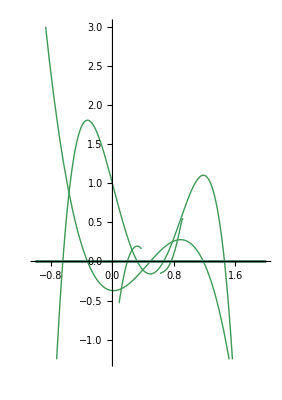

```mathematica
Plot[{Id[tForDtoBC[{0,1,0.75},{0,-1,0},{2,0,0},0.5,l,-1]]*0,tForDtoBCDisc[{0,1,0.75},{0,-1,0},{2,0,0},0.5,l]*0,(tForDtoBCRoots1[0,1,0.75,0,-1,0,2,0,0,l,0.5])*0,tForDtoBCAll[{1.2,-1,0},{1.8,-1,0},{1.0,2.2,0},0.5,l,-1],tForDtoBCDisc[{1.2,-1,0},{1.8,-1,0},{1.0,2.2,0},0.5,l]*0},{l,-1,2},PlotRange->{-1.25,3},AspectRatio->Automatic]
```

```mathematica
tForDtoBCD1[{0.5,1,0},{2,1,0.5},{3.5,-1.9,0},0.5,0,-1]
```

6.+6.69726 ⅈ

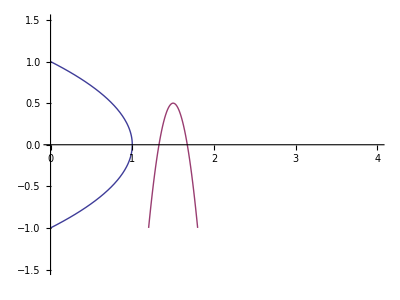

```mathematica
ParametricPlot[{bq[{0,1},{0,-1},{2,0},l],bq[{1.2,-1},{1.8,-1},{1.5,2},l]},{l,0,1},PlotRange->{{0,4},{-1.5,1.5}},AspectRatio->Automatic]
```

```mathematica
Simplify[Id[(D[Id[tForDtoP[bq[{c1x,c1y,c1z},{c2x,c2y,c2z},{hx,hy,hz},l],r,-1]],l])]]
```

-2 c1x+2 hx+(c1x+c2x-2 hx) l+(c1x-hx) l+(c2x-hx) l+(2 (c1y^2 (-1+l)^3+c1z^2 (-1+l)^3+l (c2y hy (3-4 l) l+c2z hz (3-4 l) l+(c2y^2+c2z^2) l^2+hy^2 (2-6 l+4 l^2)+hz^2 (2-6 l+4 l^2))-c1y (-1+l) (c2y (1-2 l) l+hy (1-5 l+4 l^2))-c1z (-1+l) (c2z (1-2 l) l+hz (1-5 l+4 l^2))))/(√(-(c1y (-1+l)^2+l (-2 hy (-1+l)+c2y l))^2-(c1z (-1+l)^2+l (-2 hz (-1+l)+c2z l))^2+r^2))

```mathematica
tForDtoBCRoots1[c1x_,c1y_,c1z_,c2x_,c2y_,c2z_,hx_,hy_,hz_,l_,r_]:=-2 c1x+2 hx+(c1x+c2x-2 hx) l+(c1x-hx) l+(c2x-hx) l+(2 (c1y^2 (-1+l)^3+c1z^2 (-1+l)^3+l (c2y hy (3-4 l) l+c2z hz (3-4 l) l+(c2y^2+c2z^2) l^2+hy^2 (2-6 l+4 l^2)+hz^2 (2-6 l+4 l^2))-c1y (-1+l) (c2y (1-2 l) l+hy (1-5 l+4 l^2))-c1z (-1+l) (c2z (1-2 l) l+hz (1-5 l+4 l^2))))/(√(-(c1y (-1+l)^2+l (-2 hy (-1+l)+c2y l))^2-(c1z (-1+l)^2+l (-2 hz (-1+l)+c2z l))^2+r^2))
```